# 1 D Potenital Numerical Solve

```mathematica
(ⅆ^2 R)/(ⅆ r^2)+ k^2(1- V[r]/Ε)R = 0
(R'[r+h]-R'[r])/h=-k^2(1- V[r]/Ε)R[r+h]
R'[r+h]=R'[r]-h k^2(1- V[r]/Ε)R[r+h] 
R[r+h]=R[r]+h R'[h]
```

## V

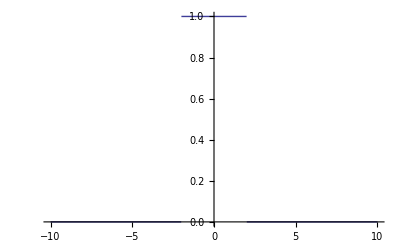

```mathematica
V[x_]:=Piecewise[{{0,x<-2},{1,-2<x<2},{0,2<x}}];
(*V[x_]:=3;*)
Plot[V[x],{x,-10,10}]
```

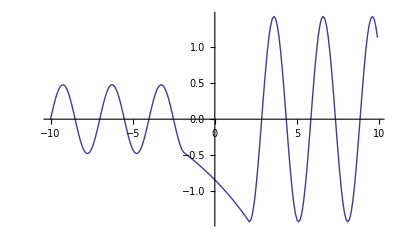

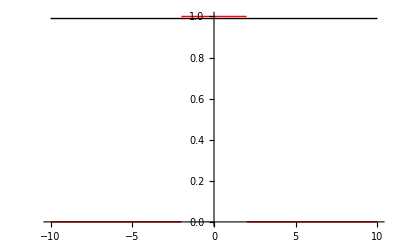

```mathematica
R0={-10,0,1};
dr=0.1;
n=200;
k=(2π)/3;
energy=0.99;
Array[U,n];
U[1]=R0;
Table[temp=U[i-1];
U[i]={
temp[[1]]+dr,
temp2=temp[[2]]+dr temp[[3]],
temp[[3]]-dr k^2(1-V[temp[[1]]]/energy)temp2
},{i,2,n,1}];
R=Table[{U[i][[1]],U[i][[2]]},{i,1,n}];
ListPlot[R,Joined->True(*,PlotRange->{{-2,2},{-5,5}}*)]
Plot[{V[x],energy},{x,-10,dr n/2},PlotStyle->{Red,Black},PlotRange->All]
```

```mathematica
Table[U[i],{i,1,n}]
```

{{-10,0,1},{-9.9,0.1,0.956135},{-9.8,0.195614,0.870329},{-9.7,0.282646,0.746347},{-9.6,0.357281,0.589626},{-9.5,0.416244,0.407041},{-9.4,0.456948,0.206601},{-9.3,0.477608,-0.00290116},{-9.2,0.477318,-0.212276},{-9.1,0.45609,-0.41234},{-9.,0.414856,-0.594316},{-8.9,0.355425,-0.750223},{-8.8,0.280402,-0.873221},{-8.7,0.19308,-0.957915},{-8.6,0.0972887,-1.00059},{-8.5,-0.00277039,-0.999376},{-8.4,-0.102708,-0.954323},{-8.3,-0.19814,-0.867409},{-8.2,-0.284881,-0.742446},{-8.1,-0.359126,-0.584916},{-8.,-0.417617,-0.401728},{-7.9,-0.45779,-0.200919},{-7.8,-0.477882,0.00870338},{-7.7,-0.477012,0.217944},{-7.6,-0.455217,0.417625},{-7.5,-0.413455,0.598986},{-7.4,-0.353556,0.754074},{-7.3,-0.278149,0.876083},{-7.2,-0.190541,0.959664},{-7.1,-0.0945742,1.00115},{-7.,0.00554069,0.998718},{-6.9,0.105413,0.952479},{-6.8,0.20066,0.86446},{-6.7,0.287106,0.738521},{-6.6,0.360958,0.580187},{-6.5,0.418977,0.396403},{-6.4,0.458617,0.195231},{-6.3,0.47814,-0.0145053},{-6.2,0.47669,-0.223605},{-6.1,0.454329,-0.422896},{-6.,0.41204,-0.603637},{-5.9,0.351676,-0.757899},{-5.8,0.275886,-0.878917},{-5.7,0.187995,-0.96138},{-5.6,0.0918565,-1.00167},{-5.5,-0.00831081,-0.998027},{-5.4,-0.108114,-0.950603},{-5.3,-0.203174,-0.861481},{-5.2,-0.289322,-0.734571},{-5.1,-0.362779,-0.575438},{-5.,-0.420323,-0.391064},{-4.9,-0.459429,-0.189535},{-4.8,-0.478383,0.0203068},{-4.7,-0.476352,0.229258},{-4.6,-0.453426,0.428153},{-4.5,-0.410611,0.608267},{-4.4,-0.349784,0.7617},{-4.3,-0.273614,0.881721},{-4.2,-0.185442,0.963065},{-4.1,-0.0891357,1.00216},{-4.,0.0110806,0.997303},{-3.9,0.110811,0.948696},{-3.8,0.205681,0.858475},{-3.7,0.291528,0.730596},{-3.6,0.364588,0.57067},{-3.5,0.421655,0.385712},{-3.4,0.460226,0.183834},{-3.3,0.478609,-0.0261075},{-3.2,0.475998,-0.234904},{-3.1,0.452508,-0.433396},{-3.,0.409168,-0.612877},{-2.9,0.347881,-0.765475},{-2.8,0.271333,-0.884495},{-2.7,0.182884,-0.964717},{-2.6,0.086412,-1.00262},{-2.5,-0.0138501,-0.996546},{-2.4,-0.113505,-0.946757},{-2.3,-0.20818,-0.855439},{-2.2,-0.293724,-0.726597},{-2.1,-0.366384,-0.565883},{-2.,-0.422972,-0.380347},{-1.9,-0.461007,-0.178126},{-1.8,-0.47882,-0.180248},{-1.7,-0.496845,-0.182449},{-1.6,-0.515089,-0.184732},{-1.5,-0.533563,-0.187096},{-1.4,-0.552272,-0.189543},{-1.3,-0.571227,-0.192074},{-1.2,-0.590434,-0.19469},{-1.1,-0.609903,-0.197392},{-1.,-0.629642,-0.200182},{-0.9,-0.64966,-0.203061},{-0.8,-0.669966,-0.206029},{-0.7,-0.690569,-0.209089},{-0.6,-0.711478,-0.212241},{-0.5,-0.732702,-0.215488},{-0.4,-0.754251,-0.21883},{-0.3,-0.776134,-0.222268},{-0.2,-0.798361,-0.225806},{-0.1,-0.820941,-0.229443},{-1.87905×10^-14,-0.843886,-0.233182},{0.1,-0.867204,-0.237025},{0.2,-0.890906,-0.240972},{0.3,-0.915004,-0.245026},{0.4,-0.939506,-0.249189},{0.5,-0.964425,-0.253462},{0.6,-0.989771,-0.257848},{0.7,-1.01556,-0.262348},{0.8,-1.04179,-0.266964},{0.9,-1.06849,-0.271698},{1.,-1.09566,-0.276552},{1.1,-1.12331,-0.28153},{1.2,-1.15147,-0.286631},{1.3,-1.18013,-0.29186},{1.4,-1.20931,-0.297219},{1.5,-1.23904,-0.302709},{1.6,-1.26931,-0.308333},{1.7,-1.30014,-0.314093},{1.8,-1.33155,-0.319993},{1.9,-1.36355,-0.326035},{2.,-1.39615,-0.332221},{2.1,-1.42937,0.294773},{2.2,-1.3999,0.908837},{2.3,-1.30901,1.48303},{2.4,-1.16071,1.99218},{2.5,-0.961492,2.41394},{2.6,-0.720099,2.72981},{2.7,-0.447118,2.92594},{2.8,-0.154524,2.99372},{2.9,0.144847,2.93018},{3.,0.437865,2.73811},{3.1,0.711676,2.42593},{3.2,0.95427,2.00735},{3.3,1.155,1.5007},{3.4,1.30507,0.928234},{3.5,1.3979,0.315047},{3.6,1.4294,-0.311959},{3.7,1.39821,-0.925281},{3.8,1.30568,-1.49802},{3.9,1.15588,-2.00504},{4.,0.955373,-2.42411},{4.1,0.712962,-2.73685},{4.2,0.439276,-2.92954},{4.3,0.146322,-2.99373},{4.4,-0.153051,-2.92659},{4.5,-0.44571,-2.73108},{4.6,-0.718818,-2.41577},{4.7,-0.960395,-1.9945},{4.8,-1.15984,-1.48573},{4.9,-1.30842,-0.911794},{5.,-1.3996,-0.297863},{5.1,-1.42938,0.329135},{5.2,-1.39647,0.941695},{5.3,-1.3023,1.51295},{5.4,-1.15101,2.01784},{5.5,-0.949222,2.43421},{5.6,-0.705801,2.74381},{5.7,-0.43142,2.93305},{5.8,-0.138115,2.99364},{5.9,0.161249,2.9229},{6.,0.453539,2.72396},{6.1,0.725935,2.40553},{6.2,0.966488,1.98158},{6.3,1.16465,1.47071},{6.4,1.31172,0.895325},{6.5,1.40125,0.280668},{6.6,1.42932,-0.3463},{6.7,1.39469,-0.958078},{6.8,1.29888,-1.52783},{6.9,1.1461,-2.03056},{7.,0.943039,-2.44423},{7.1,0.698616,-2.75067},{7.2,0.423549,-2.93646},{7.3,0.129903,-2.99344},{7.4,-0.169442,-2.91912},{7.5,-0.461354,-2.71675},{7.6,-0.733028,-2.3952},{7.7,-0.972549,-1.9686},{7.8,-1.16941,-1.45564},{7.9,-1.31497,-0.878826},{8.,-1.40285,-0.263465},{8.1,-1.4292,0.363453},{8.2,-1.39286,0.974428},{8.3,-1.29541,1.54266},{8.4,-1.14115,2.04322},{8.5,-0.936825,2.45416},{8.6,-0.691409,2.75745},{8.7,-0.415664,2.93978},{8.8,-0.121686,2.99315},{8.9,0.177629,2.91524},{9.,0.469153,2.70944},{9.1,0.740097,2.3848},{9.2,0.978577,1.95555},{9.3,1.17413,1.44052},{9.4,1.31818,0.862297},{9.5,1.40441,0.246252},{9.6,1.42904,-0.380594},{9.7,1.39098,-0.990746},{9.8,1.29191,-1.55744},{9.9,1.13616,-2.05582}}